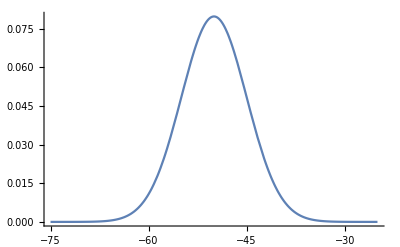

```mathematica
Plot[Abs[(1/(2*Pi*5^2)^(1/4))*Exp[-((x-(-50))^2/(4*5^2))+(I*1*x)/1]]^2,{x,-75,-25}]
(*Primeiro teste - Plotando a condição inicial do Paper do Muga pra ver se entendi o funcionamento do notebook apropriadamente*)
```

```mathematica
Integrate[(1/(2*Pi*δ^2)^(1/4))*(1/(2*Pi*δ^2)^(1/4))*Exp[-((x-x0)^2/(4*δ^2))+(I*p0*x)/h]*Exp[-(I*(p*x))],{x,-∞,∞}](*Aplicando a transformada de Fourier para calcular o Cp dessa condição inicial em Schroedinger*)
```

ConditionalExpression[(√2 √(1/δ^2) √(δ^2))/(ⅇ^(((h p-p0) (δ^2 (h p-p0)+ⅈ h x0))/h^2)), Re[δ^2]>0]

```mathematica
FullSimplify[%,Re[δ^2]>0](*Testando para ver se o programa simplifica mais*)
```

√2 √(1/δ^2) √(δ^2) ⅇ^(-((h p-p0) (δ^2 (h p-p0)+ⅈ h x0))/h^2)

```mathematica
phi (p_)=Sqrt[2] (E^(-(((h p-p0) (I h x0+(h p-p0) δ^2))/h^2)))Sqrt[(1/(δ^2))] Sqrt[(δ^2)](*Definindo uma função para o Cp pois pode ser útil posteriormente para o STS que Eduardo pediu para comparar*)
```

Set::write: Tag Times in phi p_ is Protected.

(√2 √(1/δ^2) √(δ^2))/(ⅇ^(((h p-p0) (δ^2 (h p-p0)+ⅈ h x0))/h^2))

```mathematica
Integrate[(1/(2*Pi*δ^2)^(1/4))*Sqrt[2]*Exp[-((h*p-p0)*(I*h*x0+(h*p-p0)*δ^2))/h^2]*Exp[(I*(p*x))]*Exp[-I*t*(h*p^2)/(2*m)],{p,-∞,∞}](*Voltando a transformada de Fourier com o propagador só para garantir que minha automatização ta funcionando tudo bem com essa condição inicial*)
```

ConditionalExpression[(ⅇ^((ⅈ h (m (x-x0)^2+2 p0 t x0)-2 p0 (p0 t-2 m x) δ^2)/(2 h (h t-2 ⅈ m δ^2))) (2 π)^(1/4) (h √((ⅈ h t)/m+2 δ^2) √((ⅈ m (h (x-x0)-2 ⅈ p0 δ^2)^2)/(h^2 (h t-2 ⅈ m δ^2))) Erf[(√((ⅈ m (h x-h x0-2 ⅈ p0 δ^2)^2)/(h^2 (h t-2 ⅈ m δ^2))))/(√2)]+(h (x-x0)-2 ⅈ p0 δ^2) (-2 ⅈ+Erfi[(h x-h x0-2 ⅈ p0 δ^2)/(h √((2 ⅈ h t)/m+4 δ^2))])))/((δ^2)^(1/4) √((2 ⅈ h t)/m+4 δ^2) (-ⅈ h (x-x0)-2 p0 δ^2)), 2 Re[δ^2]>Im[(h t)/m]]

```mathematica
Manipulate[Plot[Abs[(E^((I*1*(0.5*(x+50)^2+2*1*t*(-50))-2*1*(1*t-2*0.5*x)*5^2)/(2*1*(1*t-2*I*0.5*5^2)))*(2*Pi)^(1/4)*(1*Sqrt[(I*1*t)/0.5+2*5^2]*Sqrt[(I*0.5*(1*(x+50)-2*I*1*5^2)^2)/(1^2*(1*t-2*I*0.5*5^2))]*Erf[Sqrt[(I*0.5*(1*x-1*(-50)-2*I*1*5^2)^2)/(1^2*(1*t-2*I*0.5*5^2))]/Sqrt[2]]+(1*(x+50)-2*I*1*5^2)*(-2*I+Erfi[(1*x-1*(-50)-2*I*1*5^2)/(1*Sqrt[(2*I*1*t)/0.5+4*5^2])])))/((5^2)^(1/4)*Sqrt[(2*I*1*t)/0.5+4*5^2]*((-I)*1*(x+50)-2*1*5^2))]^2,{x,-75,150},PlotRange->{{-75,150},{0,0.02}}],{t,0,70}]
```

```mathematica
(*Procedendo para o paper do Muga, vamos integrar psi(x,t)*V1(x) para encontrar a distribuição de probabilidade temporal -que eventualmente em x=0 será nossa condição inicial no STS- por isso, aqui temos nossa C.I. do STS definida em formato de função*)
dndt[t_]:=NIntegrate[Abs[(E^((I*1*(0.5*(x+50)^2+2*1*t*(-50))-2*1*(1*t-2*0.5*x)*5^2)/(2*1*(1*t-2*I*0.5*5^2)))*(2*Pi)^(1/4)*(1*Sqrt[(I*1*t)/0.5+2*5^2]*Sqrt[(I*0.5*(1*(x+50)-2*I*1*5^2)^2)/(1^2*(1*t-2*I*0.5*5^2))]*Erf[Sqrt[(I*0.5*(1*x-1*(-50)-2*I*1*5^2)^2)/(1^2*(1*t-2*I*0.5*5^2))]/Sqrt[2]]+(1*(x+50)-2*I*1*5^2)*(-2*I+Erfi[(1*x-1*(-50)-2*I*1*5^2)/(1*Sqrt[(2*I*1*t)/0.5+4*5^2])])))/((5^2)^(1/4)*Sqrt[(2*I*1*t)/0.5+4*5^2]*((-I)*1*(x+50)-2*1*5^2))]^2*(2/(1*(x-1)*(x+(1/(1+I*1))))),{x,0.001,0.999}]
```

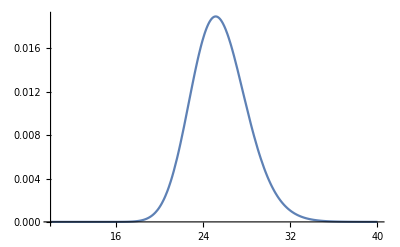

```mathematica
Plot[Abs[dndt[t]]^2,{t,10,40}](*Plot da distribuição temporal do Muga dndt em x=0, tudo funcionando exatamente como no paper*)
```

```mathematica
(*Prosseguindo com as verificações, vamos evoluir o sistema do dndt do Muga para a posição x=10 para conferir também a validade dos plots feitos previamente em python por mim*)
dndtevol[t_]:= NIntegrate[Abs[(E^((I*1*(0.5*(x+60)^2+2*1*t*(-60))-2*1*(1*t-2*0.5*x)*5^2)/(2*1*(1*t-2*I*0.5*5^2)))*(2*Pi)^(1/4)*(1*Sqrt[(I*1*t)/0.5+2*5^2]*Sqrt[(I*0.5*(1*(x+60)-2*I*1*5^2)^2)/(1^2*(1*t-2*I*0.5*5^2))]*Erf[Sqrt[(I*0.5*(1*x-1*(-60)-2*I*1*5^2)^2)/(1^2*(1*t-2*I*0.5*5^2))]/Sqrt[2]]+(1*(x+60)-2*I*1*5^2)*(-2*I+Erfi[(1*x-1*(-60)-2*I*1*5^2)/(1*Sqrt[(2*I*1*t)/0.5+4*5^2])])))/((5^2)^(1/4)*Sqrt[(2*I*1*t)/0.5+4*5^2]*((-I)*1*(x+60)-2*1*5^2))]^2*(2/(1*(x-1)*(x+(1/(1+I*1))))),{x,0.001,0.999}]
```

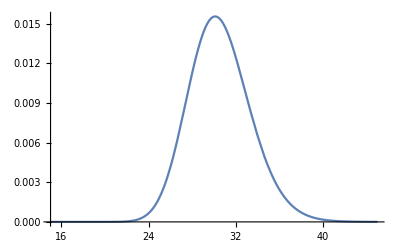

```mathematica
Plot[Abs[dndtevol[t]]^2,{t,15,45}](*perceba que o plot teve um coportamento igual/com os mesmos parametros do que eu havia feito anteriormente*)
```

```mathematica
(*Agora vamos calcular o N+, visto que o calculo do J é direto a partir do mesmo, pois J = dndt - dwell time, onde dwell time = integral N+ dt*)
nmais[t_] := NIntegrate[Abs[(E^((I*1*(0.5*(x+50)^2+2*1*t*(-50))-2*1*(1*t-2*0.5*x)*5^2)/(2*1*(1*t-2*I*0.5*5^2)))*(2*Pi)^(1/4)*(1*Sqrt[(I*1*t)/0.5+2*5^2]*Sqrt[(I*0.5*(1*(x+50)-2*I*1*5^2)^2)/(1^2*(1*t-2*I*0.5*5^2))]*Erf[Sqrt[(I*0.5*(1*x-1*(-50)-2*I*1*5^2)^2)/(1^2*(1*t-2*I*0.5*5^2))]/Sqrt[2]]+(1*(x+50)-2*I*1*5^2)*(-2*I+Erfi[(1*x-1*(-50)-2*I*1*5^2)/(1*Sqrt[(2*I*1*t)/0.5+4*5^2])])))/((5^2)^(1/4)*Sqrt[(2*I*1*t)/0.5+4*5^2]*((-I)*1*(x+50)-2*1*5^2))]^2,{x,0.001,0.999}]
```

```mathematica
dwellTime := NIntegrate[ nmais[t],{t,0.001,0.999}] (*Calculo do dwell time a partir do N+*)
```

```mathematica
j0[t_]:= Abs[dndt[t]]^2 - dwellTime (*definido J como havia mencionado anteriormente*)
```

```mathematica
Plot[j0[t],{t,10,40}](*Plotando J(0,t) - perceba que curva tem o formato esperado e está se comportando exatamente da mesma forma que dndt -como esperado- dado os parâmetros embutidos*)
```

-Graphics-

```mathematica
(*Agora, em ordem a preparar o plot do STS -primeiro como fazíamos antes, usando condição inicial temporal-*, vamos por o dndt como inicial) *)
cepsilon[ϵ_]:=NIntegrate[Abs[dndt[t]]^2 *Exp[-(I*ϵ*t)],{t,0,∞}, Method->"AdaptiveQuasiMonteCarlo"]
```

```mathematica
(*Agora, adicionando o propagador e voltando a transformada de Fourier tal qual fizemos anteriormente em schrodinger para obter a distribuição temporal STS*)
sts[x_,t_] := NIntegrate[cepsilon[ϵ]*Exp[-(I*(ϵ*t))]*Exp[(I*x*Sqrt[2*0.5*ϵ])], {ϵ,0,∞}, Method->"AdaptiveQuasiMonteCarlo"]
```

```mathematica
Plot[Abs[sts[0,t]]^2,{t,10,40}]
```

NIntegrate::inumr: The integrand ⅇ^(-ⅈ t ϵ) Abs[dndt[t]]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::itraw: Raw object 10.0006 cannot be used as an iterator.

NIntegrate::inumr: The integrand 1. ⅇ^((0.-10.0006 ⅈ) ϵ) NIntegrate[Abs[dndt[10.0006]]^2 Exp[-(ⅈ ϵ 10.0006)],{10.0006,0,∞},Method→AdaptiveQuasiMonteCarlo] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand ⅇ^(-ⅈ t ϵ) Abs[dndt[t]]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::itraw: Raw object 10.0006 cannot be used as an iterator.

General::stop: Further output of NIntegrate::itraw will be suppressed during this calculation.

-Graphics-

```mathematica
Abs[sts[0,10]]^2
```

NIntegrate::inumr: The integrand ⅇ^(-ⅈ t ϵ) dndt[t] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand ⅇ^(-ⅈ t (-1+1/(1-ϵ))) dndt[t] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Abs[NIntegrate[cepsilon[ϵ] Exp[-(ⅈ (ϵ 10))] Exp[ⅈ 0 √(2 0.5 ϵ)],{ϵ,0,∞},Method→AdaptiveQuasiMonteCarlo]]^2